# Ground State of Helium

Paul Abbott
School of Physics, Mathematics and Computing
The University of Western Australia

paul.c.abbott@uwa.edu.au

Schrödinger Equation for Helium

In atomic units (ℏ=c=m_e=1) the Schrödinger equation for a two-electron atom (with nuclear charge Z) reads

ℋ Ψ(r)=(-1/2(Δ_1+Δ_2))_T Ψ(r)+(-Z/r_1-Z/r_2+1/r_12)_V Ψ(r)=ℰ Ψ(r),

where ℋ is the Hamiltonian, 𝒯 is the kinetic energy operator, and 𝒱 is the potential energy. The interparticle coordinates — r_1, r_2, and r_12 — are defined below:

```mathematica
$FormatType=TraditionalForm;
```

```mathematica
$TextStyle={FontSize->10};
```

```mathematica
Manipulate[Module[{r1=Norm[b-a],r2=Norm[c-a],r12=Norm[c-b]},
Graphics[{Disk[a,0.2],Disk[b,0.15],Disk[c,0.15],Black,Text["r_1",(a+b)/2],Text["r_2",(a+c)/2],Text["r_12",(b+c)/2],Text["θ",(b+c)/(3 Norm[b+c])],AbsoluteThickness[0.5],Black,Line[{a,b,c,a}]}, 
ImageSize->300,
PlotRange->{{-1.2,3.2},{-1.2,3.2}},
PlotLabel->{{Subscript[r, 1]==r1,Subscript[r, 2]==r2,Subscript[r, 12]==r12},{s==r1+r2,p==r12/(r1+r2),q==(r1-r2)/r12},{r==√(r1^2+r2^2),Ω==Chop@((r1^2+r2^2-r12^2)/(2r1 r2)),y==(2r1 r2)/(r1^2+r2^2)}}]],
{{a,{0,0.}},{0,0},{0,0},Locator, Appearance->Style["Z^+",Bold,White]},
{{b,{2.,-0.5}},{-1,-1},{3,3},Locator, Appearance->Style["1",Bold,White]},
{{c,{1/2,5/2}},{-1,-1},{3,3},Locator, Appearance->Style["2",Bold,White]},
SaveDefinitions->True]
```

Δ_i is the three-dimensional Laplacian operator for electron i. In spherical polar coordinates, r=(r,θ,ϕ), the Laplacian reads

Δ=1/r^2(∂(r^2 ∂/(∂r)))/(∂r)-1/r^2 l^2(θ,ϕ),

where the angular part, l^2(θ,ϕ), is the square of the (total) angular momentum operator,

l^2(θ,ϕ)=-(1/(sin(θ))(∂(sin(θ) ∂/(∂θ)))/(∂θ)+1/(sin^2(θ))∂^2/(∂ϕ^2)).

For spherically symmetric states (s-states), one has

Δ_1+Δ_2=1/r_1^2(∂(r_1^2 ∂/(∂r_1)))/(∂r_1)+1/r_2^2(∂(r_2^2 ∂/(∂r_2)))/(∂r_2)-(1/r_1^2+1/r_2^2)l^2(θ),

where r_1·r_2=r_1 r_2 cos(θ) (i.e., θ is the angle between r_1 and r_2) and

l^2(θ)=-1/(sin(θ))(∂(sin(θ) ∂/(∂θ)))/(∂θ).

Perturbation Calculation

Considering the inter-electron potential, 1/r_12, as a perturbation, the Hamiltonian  can be written as

ℋ==(-1/2(Δ_1+Δ_2)-Z/r_1-Z/r_2)_(ℋ^(0))+(1/r_12)_(⏟_ℋ'),

where

ℋ^(0)==(-1/2 Δ_1-Z/r_1)_ℋ_1_(-1/2 Δ_2-Z/r_2)_ℋ_2_,

and

ℋ'==1/r_12·

To zeroth order, the Hamiltonian is simply separated into the sum of two single-particle (hydrogenic) operators, ℋ^(0)=ℋ_1+ℋ_2. Hence the (unnormalized) ground state of the a two-electron atom can be approximated by a product of hydrogenic functions (with nuclear charge Z),

ψ^(0)=ⅇ^(-Z (r_1+r_2)),

and the energy is the sum of the two hydrogenic (ground-state) energies, i.e.,

ℋ^(0)ψ^(0)=ℰ^(0)ψ^(0) where ℰ^(0)=-Z^2/2-Z^2/2=-Z^2.

Exercise. Show that ψ^(0) is an eigenfunction of ℋ^(0) with corresponding zeroth order energy, ℰ^(0)=-Z^2. [2]

```mathematica
Subscript[ψ, 0]=ⅇ^(-Z (Subscript[r, 1]+Subscript[r, 2]));
```

```mathematica
-1/2 (1/Subscript[r, 1]^2(∂(Subscript[r, 1]^2 (∂Subscript[ψ, 0])/(∂Subscript[r, 1])))/(∂Subscript[r, 1])+1/Subscript[r, 2]^2(∂(Subscript[r, 2]^2 (∂Subscript[ψ, 0])/(∂Subscript[r, 2])))/(∂Subscript[r, 2]))-(Z/Subscript[r, 1]+Z/Subscript[r, 2]) Subscript[ψ, 0]==-Z^2 Subscript[ψ, 0]//Simplify
```

True

Exercise. What is the helium ground state energy of the zeroth order approximation? Compare this to the exact value of -2.904...  [2]

```mathematica
-Z^2/.Z->2
```

-4

This result is, as expected, lower than the exact value because it ignores the electron-electron interaction.

### Section.Subsection. First-order perturbation energy

The first-order perturbation energy, ℰ^(1), is ℰ^(1)=ℰ^(0)+Δℰ, where the energy shift is given by

Δℰ=⟨ψ^(0)|1/r_12|ψ^(0)⟩/⟨ψ^(0)|ψ^(0)⟩.

### Section.Subsection. “Standard method” for computing Δℰ

The usual textbook computation of Δℰ is as follows. We need to compute

⟨ψ^(0)|1/r_12|ψ^(0)⟩/⟨ψ^(0)|ψ^(0)⟩=(∫∫ⅇ^(-Z (r_1+ r_2))1/r_12 ⅇ^(-Z (r_1+ r_2))ⅆ r_1ⅆ r_2)/(∫∫ⅇ^(-2Z (r_1+ r_2))ⅆ r_1ⅆ r_2).

#### Generating Function

Since r_12^2=r_1^2+r_2^2-2 r_1 r_2 cos(θ), we can expand the perturbation using the generating function for Legendre polynomials:

1/r_12=1/(√(r_1^2+r_2^2-2 r_1 r_2 cos(θ)))=1/(r_>√(1+((r_<)/(r_>))^2-2((r_<)/(r_>))cos(θ)))=1/(r_>)∑_(l=0)^∞ ((r_<)/(r_>))^l P_l(cos(θ)),

where r_>=max(r_1,r_2), r_<=min(r_1,r_2) and cos(θ) is the angle between r_1 and r_2.

Since r_1·r_2==r_1 r_2 cos(θ)⇒u_1·u_2==cos(θ) it is easy to show that

cos(θ)=cos(θ_1)cos(θ_2)+sin(θ_1)sin(θ_2)cos(ϕ_2-ϕ_1).

#### Addition Theorem

Using the addition theorem

P_l(cos(θ))=(4π)/(2l+1)∑_(m=-l)^l (Y_l^m(θ_1,ϕ_1))^* Y_l^m(θ_2,ϕ_2),

and the orthonormality of the spherical harmonics, Y_l^m(θ,ϕ), the angular integrals are trivial

∫_0^(2π) ∫_0^π ∫_0^(2π) ∫_0^π P_l(cos(θ))sin(θ_1)ⅆ θ_1ⅆ ϕ_1sin(θ_2)ⅆ θ_2ⅆ ϕ_2
=(4π)/(2l+1)∑_(m=-l)^l (∫_0^(2π) ∫_0^π (Y_l^m(θ_1,ϕ_1))^* sin(θ_1)ⅆ θ_1ⅆ ϕ_1)_((2 √π δ_(l,0)δ_(m,0))_)(∫_0^(2π) ∫_0^π Y_l^m(θ_2,ϕ_2) sin(θ_2)ⅆ θ_2ⅆ ϕ_2)_(2 √π δ_(l,0)δ_(m,0))=(4π)^2 δ_(l,0).

We have used the fact that Y_0^0(θ,ϕ) is a constant,

```mathematica
Subscript[Y, 0]^0(θ,ϕ)
```

1/(2 √π)

and introduced this term into both integrals so that the orthonormality condition can be applied.

Exercise. Verify the addition theorem for 0<=l<=6. [2]

Define cos(θ) (using TagSet to associate the assignment with the symbol θ):

```mathematica
θ/:cos(θ)=cos(Subscript[θ, 1])cos(Subscript[θ, 2])+sin(Subscript[θ, 1])sin(Subscript[θ, 2])cos(Subscript[ϕ, 2]-Subscript[ϕ, 1]);
```

Verify the addition theorem for 0<=l<=6:

```mathematica
Table[{l,Subscript[P, l](cos(θ))-(4π)/(2l+1)∑_(m=-l)^l Conjugate[Subscript[Y, l]^m(Subscript[θ, 1],Subscript[ϕ, 1])] Subscript[Y, l]^m(Subscript[θ, 2],Subscript[ϕ, 2])},{l,0,6}]//ComplexExpand//Simplify
```

(0 | 0
1 | 0
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0)

#### Perturbation Energy

Hence the six-fold integration reduces to a two-dimensional integral, with the inner integral split into two cases.

⟨ψ^(0)|1/r_12|ψ^(0)⟩=(4π)^2  ∫_0^∞ ⅇ^(-2Z r_1) (1/r_1∫_0^r_1 ⅇ^(-2Z r_2)r_2^2 ⅆ r_2+∫_r_1^∞ ⅇ^(-2Z r_2)1/r_2 r_2^2 ⅆ r_2)r_1^2 ⅆ r_1.

Exercise. Compute ℐ=⟨ψ^(0)|1/r_12|ψ^(0)⟩. [1]

Computing this integral is straightforward:

```mathematica
SetOptions[Integrate,Assumptions->{Z>0}];
```

```mathematica
ℐ=(4π)^2  ∫_0^∞ ⅇ^(-2Z Subscript[r, 1]) (1/Subscript[r, 1]∫_0^Subscript[r, 1] ⅇ^(-2Z Subscript[r, 2])Subscript[r, 2]^2 ⅆ Subscript[r, 2]+∫_Subscript[r, 1]^∞ ⅇ^(-2Z Subscript[r, 2])1/Subscript[r, 2] Subscript[r, 2]^2 ⅆ Subscript[r, 2])Subscript[r, 1]^2 ⅆ Subscript[r, 1]
```

(5 π^2)/(8 Z^5)

Exercise. Compute the normalization integral 𝒩=⟨ψ^(0)|ψ^(0)⟩. [1]

```mathematica
𝒩=(4π)^2 (∫_0^∞ ⅇ^(-2Z Subscript[r, 1]) Subscript[r, 1]^2 ⅆ Subscript[r, 1])(∫_0^∞ ⅇ^(-2Z Subscript[r, 2])Subscript[r, 2]^2 ⅆ Subscript[r, 2])
```

π^2/Z^6

Exercise. Determine Δℰ. [1]

```mathematica
Δℰ=ℐ/𝒩
```

(5 Z)/8

### Section.Subsection. Perimetric Coordinates

The matrix element of a general operator, 𝔒, can be computed from the integral

⟨ψ|𝔒|ψ⟩=∫∫ψ^*𝔒 ψ r_12 ⅆ r_1ⅆ r_2

In interparticle coordinates this reads

⟨ψ|𝔒|ψ⟩=8 π^2∫_0^∞ ∫_0^∞ ∫_(|r_1-r_2|)^(r_1+r_2) ψ^*𝔒 ψ r_1 r_2 r_12 ⅆ r_12ⅆ r_2ⅆ r_1≡8 π^2 (∫_0^∞ ∫_0^r_1 ∫_(r_1-r_2)^(r_1+r_2) ψ^*𝔒 ψ r_1 r_2 r_12 ⅆ r_12ⅆ r_2ⅆ r_1+∫_0^∞ ∫_r_1^∞ ∫_(r_2-r_1)^(r_1+r_2) ψ^*𝔒 ψ r_1 r_2 r_12 ⅆ r_12ⅆ r_2ⅆ r_1)

There is a simpler way: interparticle coordinates suffer from the fact that their variables satisfy triangular inequalities, |r_1-r_2|≤r_12<=r_1+r_2, complicating the integration. This can be avoided by introducing perimetric coordinates (Coolidge and James 1937), which treat all three particles on an equal footing:

x=r_2+r_12-r_1, y=r_1+r_12-r_2, z=r_1+r_2-r_12,

with inverse:

r_1=(y+z)/2,r_2=(z+x)/2, r_12=(x+y)/2.

The matrix element of a general operator, 𝔒, reads

⟨ψ|𝔒|ψ⟩=π^2/4∫_0^∞ ∫_0^∞ ∫_0^∞ (x+y)(y+z)(z+x)ψ^*𝔒 ψ ⅆx ⅆyⅆz.

In particular, with the exponential ansatz,

Φ(r)=ⅇ^(-λ_1 r_1-λ_2 r_2-λ_12 r_12),

the general matrix element is trivial to compute:

⟨Φ|1/(r_1 r_2 r_12)|Φ⟩=(2 π^2)/((λ_1+λ_2)(λ_1+λ_12)(λ_2+λ_12)).

Indeed, computing this matrix element integral is immediate:

```mathematica
ℐ=Assuming[Subscript[λ, 1]+Subscript[λ, 2]>0,2 π^2∫_0^∞ ∫_0^∞ ∫_0^∞ exp(-Subscript[λ, 1] (y+z)-Subscript[λ, 2] (x+z)-Subscript[λ, 12] (x+y)) ⅆx ⅆyⅆz//ComplexExpand]
```

(2 π^2)/((λ_1+λ_2) (λ_1+λ_12) (λ_2+λ_12))

### Section.Subsection. Parametric Differentiation

The importance of this integral is that matrix elements of any combination of integral powers (≥-1) of the interparticle coordinates can be obtained by differentiation with respect to the parameters, λ_i.  Moreover, this general integral permits the examination of a whole class of zeroth order approximations (including exponential terms of the above form multiplied by polynomials in the interparticle coordinates).

Observe that

∂_λ_i ⟨Φ|1/(r_1 r_2 r_12)|Φ⟩=-2⟨Φ|r_i/(r_1 r_2 r_12)|Φ⟩, i=1,2,12.

and, in general

∂^(i+j+m+3)/(∂λ_1^(i+1)∂λ_2^(j+1)∂λ_12^(m+1))⟨Φ|1/(r_1 r_2 r_12)|Φ⟩=(-2)^(i+j+m+3)⟨Φ|r_1^i r_2^j r_12^m|Φ⟩.

Define this general matrix element (after moving the power of 2 to the left-hand side of the equation) as

```mathematica
⟨i_,j_,m_⟩:=⟨i,j,m⟩=Factor[1/(-2)^(i+j+m+3)(∂^(i+j+m+3) ℐ)/(∂Subscript[λ, 1]^(i+1) ∂Subscript[λ, 2]^(j+1) ∂Subscript[λ, 12]^(m+1))]
```

#### Normalisation

Exercise. Use the general matrix element to compute the normalization of the zeroth order approximation. Hint: you need to compute ⟨ψ^(0)|ψ^(0)⟩. After differentiation, the values of the matrix element with the zeroth-order wavefunction defined above can be easily obtained by the substitution (replacement rule) {λ_1→Z,λ_2→Z,λ_12→0}. [1]

```mathematica
⟨0,0,0⟩/.{Subscript[λ, 1]->Z,Subscript[λ, 2]->Z,Subscript[λ, 12]->0}//Simplify
```

π^2/Z^6

#### Electron-electron interaction

Exercise. Use the general matrix element to compute the value of the electron-electron perturbation Δℰ. [3]

```mathematica
⟨0,0,-1⟩/⟨0,0,0⟩/.{Subscript[λ, 1]->Z,Subscript[λ, 2]->Z,Subscript[λ, 12]->0}//Simplify
```

(5 Z)/8

#### Total energy

Exercise. Using the value you obtained for the electron-electron perturbation energy, what is the first-order energy, E^(1)? [2]

The first-order perturbation energy, ℰ^(1), is ℰ^(1)=ℰ^(0)+Δℰ=-Z^2+(5Z)/8.

Variational Calculation

### Section.Subsection. Using Interparticle Coordinates

In interparticle coordinates the (s-state) kinetic energy operator, 𝒯=-1/2(Δ_1+Δ_2), reads

```mathematica
𝒯(ψ_):=-1/2 ((∂^2 ψ)/(∂Subscript[r, 1]^2)+(∂^2 ψ)/(∂Subscript[r, 2]^2)+2(∂^2 ψ)/(∂Subscript[r, 12]^2)+2/Subscript[r, 1](∂ψ)/(∂Subscript[r, 1])+2/Subscript[r, 2](∂ψ)/(∂Subscript[r, 2])+4/Subscript[r, 12](∂ψ)/(∂Subscript[r, 12])+(Subscript[r, 1]^2-Subscript[r, 2]^2+Subscript[r, 12]^2)/(Subscript[r, 1] Subscript[r, 12])(∂^2 ψ)/(∂Subscript[r, 1] ∂Subscript[r, 12])+(Subscript[r, 2]^2-Subscript[r, 1]^2+Subscript[r, 12]^2)/(Subscript[r, 2] Subscript[r, 12])(∂^2 ψ)/(∂Subscript[r, 2] ∂Subscript[r, 12]))
```

the potential energy operator, 𝒱, is

```mathematica
𝒱=-Z/Subscript[r, 1]-Z/Subscript[r, 2]+1/Subscript[r, 12];
```

and the Hamiltonian, ℋ, is

```mathematica
ℋ(ψ_):=𝒯(ψ)+𝒱 ψ
```

Using the generating integral above we can compute matrix elements of any zeroth order approximation consisting of a linear combination of terms of the form  P(r_1,r_2,r_12)ⅇ^(-λ_1 r_1-λ_2 r_2-λ_12 r_12), where P(r_1,r_2,r_12) is a polynomial in the interparticle coordinates.

Exercise. Consider the trial wavefunction

```mathematica
Subscript[ψ, 0]=ⅇ^(-Z Subscript[r, 1]-Z Subscript[r, 2]+Subscript[r, 12]/2) ;
```

Use ⟨i,j,k⟩ to compute the normalisation integral ⟨ψ_0|ψ_0⟩. [2]

```mathematica
Λ={Subscript[λ, 1]->Z,Subscript[λ, 2]->Z,Subscript[λ, 12]->-1/2};
```

```mathematica
Simplify[⟨0,0,0⟩/.Λ]
```

(π^2 (32 Z^2-10 Z+1))/(Z^3 (2 Z-1)^5)

Exercise. Compute the matrix element ℰ[Z]=⟨ψ_0|ℋ|ψ_0⟩/⟨ψ_0|ψ_0⟩ and determine the approximation to the helium ground-state energy, i.e., ℰ[2], for this trial wavefunction.  Compare your result with the non-relativistic ground-state energy for helium, i.e., -2.903724377034 a.u.  [6]

Hint: you may find it advantageous to compute the local energy, ℋ[ψ_0]/ψ_0, since ⟨ψ_0|ℋ|ψ_0⟩≡⟨ψ_0|ℋ[ψ_0]/ψ_0|ψ_0⟩.

Aside: the quantity ℋ[ψ]/ψ is known as the local energy because, if  ψ were an exact solution to the Schrödinger equation, ℋ[ψ]/ψ=ℰ.  However, for approximate wavefunctions such as ψ_0, ℋ[ψ_0]/ψ_0 is a function of the interparticle coordinates.

Here is the local energy:

```mathematica
Expand[(ℋ(Subscript[ψ, 0]))/Subscript[ψ, 0]]
```

-Z^2+(r_12 Z)/(4 r_1)+(r_12 Z)/(4 r_2)-(r_2^2 Z)/(4 r_1 r_12)+(r_1 Z)/(4 r_12)+(r_2 Z)/(4 r_12)-(r_1^2 Z)/(4 r_2 r_12)-1/4

```mathematica
Collect[%,Z,Factor]
```

-Z^2-((r_1+r_2) (r_1-r_2-r_12) (r_1-r_2+r_12) Z)/(4 r_1 r_2 r_12)-1/4

Using pattern-matching,

```mathematica
ℰ(Z_)=Factor[(Expand[Subscript[r, 1]^i Subscript[r, 2]^j Subscript[r, 12]^k %]/.Subscript[r, 1]^(i+l_.) Subscript[r, 2]^(j+m_.) Subscript[r, 12]^(k+n_.)->⟨l,m,n⟩)/⟨0,0,0⟩/.Λ]
```

-((2 Z-1) (64 Z^3-28 Z^2+8 Z-1))/(4 (32 Z^2-10 Z+1))

and for helium we obtain

```mathematica
ℰ(2.)
```

-2.8555

The non-relativistic energy is

```mathematica
Subscript[ℰ, NR]=-2.903724377034;
```

so this answer is too high by (ℰ_NR-ℰ(2))/ℰ_NR≈1.661%.

```mathematica
(Subscript[ℰ, NR]-ℰ(2))/Subscript[ℰ, NR]//PercentForm
```

1.661%

Exercise. Can you conclude whether H^- is bound? Hint: is ℰ[1] less than the ionization energy of hydrogen? [2]

```mathematica
ℰ(1.)
```

-0.467391

Since the ionization energy of hydrogen is -1/2 and this energy is an upper bound for the H^- ground state energy, we cannot determine by the energy obtained from our approximate wave function whether H^- is bound.

Exercise. Produce a plot of ℰ[Z] versus Z for two-electron atoms with nuclear charge 1≤Z≤5. [1]

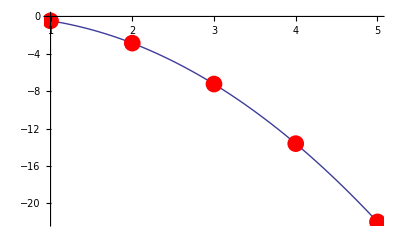

```mathematica
Plot[ℰ(Z),{Z,1,5},Epilog->{Hue[1],PointSize[0.03],Point/@Table[{Z,ℰ(Z)},{Z,1,5}]}]
```

Exercise. Now consider the more general trial wavefunction

```mathematica
Subscript[ψ, 0]=ⅇ^(-λ (Subscript[r, 1]+Subscript[r, 2])-Subscript[λ, 12] Subscript[r, 12]);
```

Compute the matrix element ℰ_(λ,ζ)[𝒵]=⟨ψ_0|ℋ|ψ_0⟩/⟨ψ_0|ψ_0⟩.  Use the variational method to numerically determine the values of λ and ζ that give the lowest ground-state energy for helium. [7]

Hint: use FindMinimum to find values of λ and ζ such that ℰ_(λ,ζ)[2] is a minimum. Explain why you expect this minimum energy to be lower than that obtained in question Exercise.

```mathematica
Λ={Subscript[λ, 1]->λ,Subscript[λ, 2]->λ,Subscript[λ, 12]->ζ};
```

```mathematica
Subscript[ℰ, λ_,ζ_](Z_)=Factor[(Expand[(Subscript[r, 1]^i Subscript[r, 2]^j Subscript[r, 12]^k ℋ(Subscript[ψ, 0]))/Subscript[ψ, 0]]/.Subscript[r, 1]^(i+l_.) Subscript[r, 2]^(j+m_.) Subscript[r, 12]^(k+n_.)->⟨l,m,n⟩)/⟨0,0,0⟩/.Λ]
```

((ζ+λ) (ζ^3+4 λ ζ^2+ζ^2+7 λ^2 ζ-4 Z λ ζ+4 λ ζ+8 λ^3-16 Z λ^2+5 λ^2))/(ζ^2+5 λ ζ+8 λ^2)

```mathematica
FindMinimum[Subscript[ℰ, λ,ζ](2),{λ,2},{ζ,-1/2}]
```

{-2.88962,{λ→1.85809,ζ→-0.254746}}

This answer is, as expected, lower than that obtained in problem Exercise because ψ_0=ⅇ^(-λ (r_1+r_2)-ζ r_12) includes the previous example as a special case and we now have two variational parameters. The minimum energy is quite close to the “exact” value: (ℰ_NR-ℰ_(ζ,λ)(2))/ℰ_NR≈"0.4858%".

```mathematica
(Subscript[ℰ, NR]-First[%])/Subscript[ℰ, NR]
```

0.4858%

Exercise. Using the more general trial wavefunction, can you now conclude that H^- is bound? [2]

```mathematica
FindMinimum[Subscript[ℰ, λ,ζ](1),{λ,1},{ζ,-1/2}]
```

{-0.507901,{λ→0.852833,ζ→-0.225888}}

Since the variational energy is less than the ionization energy of hydrogen we can conclude that H^- is (very weakly) bound.

Exercise. Produce a table of optimal values of ℰ_(λ,ζ)(Z) for 1≤Z≤10. What patterns do you observe in the values of the energies and the parameters? [2]

```mathematica
direct=Table[{Z,FindMinimum[Subscript[ℰ, λ,ζ](Z), {λ,Z},{ζ,1},WorkingPrecision->20]},{Z,1,10}]
```

(1 | {-0.50790086554752972515,{λ→0.8528331207916526363,ζ→-0.2258882239904120242}}
2 | {-2.8896182053521416273,{λ→1.858088240099541622,ζ→-0.25474600288672896555}}
3 | {-7.2668186951613787068,{λ→2.8599478651383060476,ζ→-0.26406385416973695456}}
4 | {-13.64290901037936991,{λ→3.8608935933225588123,ζ→-0.268647150353088769}}
5 | {-22.01855970510964267,{λ→4.8614655323585538903,ζ→-0.27137076349495331604}}
6 | {-32.393991975458545224,{λ→5.8618485623153311365,ζ→-0.27317505264653165285}}
7 | {-44.769299971030275403,{λ→6.8621229622312358601,ζ→-0.2744580800106413393}}
8 | {-59.144530539124451834,{λ→7.8623291867117323677,ζ→-0.2754171533196436717}}
9 | {-75.519709612402126978,{λ→8.8624898277516841066,ζ→-0.27616118210694649503}}
10 | {-93.894852707147566176,{λ→9.8626184908503920539,ζ→-0.27675518661878904509}})

The energies are going roughly as Z^-2. The parameters appear to be converging to λ≈Z-0.14 and ζ≈-0.28.

### Section.Subsection. Linear Combinations

It is straightforward to compute matrix elements of any linear combination of terms of the form  P(r_1,r_2,r_12)ⅇ^(-λ_1 r_1-λ_2 r_2-λ_12 r_12), where P(r_1,r_2,r_12) is a polynomial in the interparticle coordinates.

Exercise. Consider the symmetric trial wavefunction

```mathematica
Subscript[ψ, 0]=ⅇ^(-α Subscript[r, 1]-β Subscript[r, 2]-γ Subscript[r, 12]) ;
```

```mathematica
Subscript[ψ, 0]=(Subscript[ψ, 0]+(Subscript[ψ, 0]/.{Subscript[r, 1]->Subscript[r, 2],Subscript[r, 2]->Subscript[r, 1]}))/2
```

1/2 (ⅇ^(-β r_1-α r_2-γ r_12)+ⅇ^(-α r_1-β r_2-γ r_12))

Compute the normalisation integral ⟨ψ_0|ψ_0⟩. [2]

```mathematica
Expand[Subscript[ψ, 0]^2]//.a_ Subscript[r, i_]+b_ Subscript[r, i_]:>(a+b)Subscript[r, i]
```

1/4 ⅇ^(-2 β r_1-2 α r_2-2 γ r_12)+1/2 ⅇ^((-α-β) r_1+(-α-β) r_2-2 γ r_12)+1/4 ⅇ^(-2 α r_1-2 β r_2-2 γ r_12)

```mathematica
Expand[Subscript[r, 1]^i Subscript[r, 2]^j Subscript[r, 12]^k %]/.d_. Subscript[r, 1]^(i+l_.) Subscript[r, 2]^(j+m_.) Subscript[r, 12]^(k+n_.)ⅇ^(a_ Subscript[r, 1]+b_ Subscript[r, 2]+c_ Subscript[r, 12]):>(d⟨l,m,n⟩/.{Subscript[λ, 1]->-a/2,Subscript[λ, 2]->-b/2,Subscript[λ, 12]->-c/2})
```

(π^2 (α^3+3 β α^2+3 γ α^2+3 β^2 α+3 γ^2 α+7 β γ α+β^3+γ^3+3 β γ^2+3 β^2 γ))/(2 (α+β)^3 (α+γ)^3 (β+γ)^3)+(π^2 ((α+β)^3+13/4 γ (α+β)^2+3 γ^2 (α+β)+γ^3))/(2 (α+β)^3 ((α+β)/2+γ)^6)

```mathematica
Subscript[𝒩, α_,β_,γ_]=Simplify/@%
```

(8 π^2 (4 α^2+8 β α+5 γ α+4 β^2+2 γ^2+5 β γ))/((α+β)^3 (α+β+2 γ)^5)+(π^2 (α^3+3 (β+γ) α^2+(3 β^2+7 γ β+3 γ^2) α+(β+γ)^3))/(2 (α+β)^3 (α+γ)^3 (β+γ)^3)

As a check

```mathematica
Subscript[𝒩, Z,Z,-1/2]//Factor
```

(π^2 (32 Z^2-10 Z+1))/(Z^3 (2 Z-1)^5)

```mathematica
⟨0,0,0⟩/.{Subscript[λ, 1]->Z,Subscript[λ, 2]->Z,Subscript[λ, 12]->-1/2}//Factor
```

(π^2 (32 Z^2-10 Z+1))/(Z^3 (2 Z-1)^5)

Exercise. Compute the matrix element ℰ[Z]=⟨ψ_0|ℋ|ψ_0⟩/⟨ψ_0|ψ_0⟩ and determine the approximation to the helium ground-state energy for this trial wavefunction. [6]

To compute ⟨ψ_0|ℋ|ψ_0⟩, we need

```mathematica
Collect[Expand[Subscript[ψ, 0] ℋ(Subscript[ψ, 0])]//.a_ Subscript[r, i_]+b_ Subscript[r, i_]:>(a+b)Subscript[r, i],{ⅇ^_},Expand]
```

ⅇ^(-2 β r_1-2 α r_2-2 γ r_12) (-α^2/8-(γ r_12 α)/(8 r_2)+α/(4 r_2)-(γ r_2 α)/(8 r_12)+(γ r_1^2 α)/(8 r_2 r_12)-β^2/8-γ^2/4-(β γ r_12)/(8 r_1)-Z/(4 r_1)+β/(4 r_1)-Z/(4 r_2)+(β γ r_2^2)/(8 r_1 r_12)+γ/(2 r_12)-(β γ r_1)/(8 r_12)+1/(4 r_12))+ⅇ^(-2 α r_1-2 β r_2-2 γ r_12) (-α^2/8-(γ r_12 α)/(8 r_1)+α/(4 r_1)+(γ r_2^2 α)/(8 r_1 r_12)-(γ r_1 α)/(8 r_12)-β^2/8-γ^2/4-(β γ r_12)/(8 r_2)-Z/(4 r_1)-Z/(4 r_2)+β/(4 r_2)+γ/(2 r_12)-(β γ r_2)/(8 r_12)+(β γ r_1^2)/(8 r_2 r_12)+1/(4 r_12))+ⅇ^((-α-β) r_1+(-α-β) r_2-2 γ r_12) (-α^2/4-(γ r_12 α)/(8 r_1)-(γ r_12 α)/(8 r_2)+α/(4 r_1)+α/(4 r_2)+(γ r_2^2 α)/(8 r_1 r_12)-(γ r_1 α)/(8 r_12)-(γ r_2 α)/(8 r_12)+(γ r_1^2 α)/(8 r_2 r_12)-β^2/4-γ^2/2-(β γ r_12)/(8 r_1)-(β γ r_12)/(8 r_2)-Z/(2 r_1)+β/(4 r_1)-Z/(2 r_2)+β/(4 r_2)+(β γ r_2^2)/(8 r_1 r_12)+γ/r_12-(β γ r_1)/(8 r_12)-(β γ r_2)/(8 r_12)+(β γ r_1^2)/(8 r_2 r_12)+1/(2 r_12))

Using pattern-matching,

```mathematica
Expand[Subscript[r, 1]^i Subscript[r, 2]^j Subscript[r, 12]^k %]/.d_. Subscript[r, 1]^(i+l_.) Subscript[r, 2]^(j+m_.) Subscript[r, 12]^(k+n_.)ⅇ^(a_ Subscript[r, 1]+b_ Subscript[r, 2]+c_ Subscript[r, 12]):>(d⟨l,m,n⟩/.{Subscript[λ, 1]->-a/2,Subscript[λ, 2]->-b/2,Subscript[λ, 12]->-c/2})
```

-(π^2 (α^3+3 β α^2+3 γ α^2+3 β^2 α+3 γ^2 α+7 β γ α+β^3+γ^3+3 β γ^2+3 β^2 γ) α^2)/(4 (α+β)^3 (α+γ)^3 (β+γ)^3)-(π^2 ((α+β)^3+13/4 γ (α+β)^2+3 γ^2 (α+β)+γ^3) α^2)/(4 (α+β)^3 ((α+β)/2+γ)^6)+(3 π^2 γ (α+2 β+γ) (α^2+2 β α+2 β^2+γ^2+2 β γ) α)/(8 (α+β)^4 (α+γ) (β+γ)^4)+(π^2 (α^2+2 β α+2 γ α+β^2+γ^2+3 β γ) α)/(2 (α+β)^2 (α+γ)^2 (β+γ)^3)+(3 π^2 γ (α+β+(α+β)/2+γ) (5/4 (α+β)^2+γ (α+β)+γ^2) α)/(8 (α+β)^4 ((α+β)/2+γ)^5)+(π^2 ((α+β)^2+5/2 γ (α+β)+γ^2) α)/(2 (α+β)^2 ((α+β)/2+γ)^5)-(π^2 γ (3 α^3+12 β α^2+9 γ α^2+8 β^2 α+9 γ^2 α+16 β γ α+2 β^3+3 γ^3+6 β γ^2+4 β^2 γ) α)/(8 (α+β)^4 (α+γ)^3 (β+γ)^2)-(π^2 γ (3 α^3+6 β α^2+9 γ α^2+4 β^2 α+9 γ^2 α+16 β γ α+2 β^3+3 γ^3+12 β γ^2+8 β^2 γ) α)/(8 (α+β)^2 (α+γ)^3 (β+γ)^4)-(π^2 γ (25/8 (α+β)^3+29/4 γ (α+β)^2+15/2 γ^2 (α+β)+3 γ^3) α)/(8 (α+β)^4 ((α+β)/2+γ)^5)-(π^2 γ (15/8 (α+β)^3+33/4 γ (α+β)^2+21/2 γ^2 (α+β)+3 γ^3) α)/(8 (α+β)^2 ((α+β)/2+γ)^7)+(3 π^2 β γ (2 α+β+γ) (2 α^2+2 β α+2 γ α+β^2+γ^2))/(8 (α+β)^4 (α+γ)^4 (β+γ))+(π^2 γ (α^2+3 β α+2 γ α+β^2+γ^2+2 β γ))/((α+β)^3 (α+γ)^2 (β+γ)^2)+(π^2 (α^2+3 β α+2 γ α+β^2+γ^2+2 β γ))/(2 (α+β)^3 (α+γ)^2 (β+γ)^2)-(π^2 Z (α^2+2 β α+3 γ α+β^2+γ^2+2 β γ))/(2 (α+β)^2 (α+γ)^3 (β+γ)^2)+(π^2 β (α^2+2 β α+3 γ α+β^2+γ^2+2 β γ))/(2 (α+β)^2 (α+γ)^3 (β+γ)^2)-(π^2 Z (α^2+2 β α+2 γ α+β^2+γ^2+3 β γ))/(2 (α+β)^2 (α+γ)^2 (β+γ)^3)+(3 π^2 β γ (α+β+(α+β)/2+γ) (5/4 (α+β)^2+γ (α+β)+γ^2))/(8 (α+β)^4 ((α+β)/2+γ)^5)+(π^2 γ (5/4 (α+β)^2+2 γ (α+β)+γ^2))/((α+β)^3 ((α+β)/2+γ)^4)+(π^2 (5/4 (α+β)^2+2 γ (α+β)+γ^2))/(2 (α+β)^3 ((α+β)/2+γ)^4)-(π^2 Z ((α+β)^2+5/2 γ (α+β)+γ^2))/((α+β)^2 ((α+β)/2+γ)^5)+(π^2 β ((α+β)^2+5/2 γ (α+β)+γ^2))/(2 (α+β)^2 ((α+β)/2+γ)^5)-(π^2 γ^2 (α^3+3 β α^2+3 γ α^2+3 β^2 α+3 γ^2 α+7 β γ α+β^3+γ^3+3 β γ^2+3 β^2 γ))/(2 (α+β)^3 (α+γ)^3 (β+γ)^3)-(π^2 β^2 (α^3+3 β α^2+3 γ α^2+3 β^2 α+3 γ^2 α+7 β γ α+β^3+γ^3+3 β γ^2+3 β^2 γ))/(4 (α+β)^3 (α+γ)^3 (β+γ)^3)-(π^2 γ^2 ((α+β)^3+13/4 γ (α+β)^2+3 γ^2 (α+β)+γ^3))/(2 (α+β)^3 ((α+β)/2+γ)^6)-(π^2 β^2 ((α+β)^3+13/4 γ (α+β)^2+3 γ^2 (α+β)+γ^3))/(4 (α+β)^3 ((α+β)/2+γ)^6)-(π^2 β γ (2 α^3+8 β α^2+4 γ α^2+12 β^2 α+6 γ^2 α+16 β γ α+3 β^3+3 γ^3+9 β γ^2+9 β^2 γ))/(8 (α+β)^4 (α+γ)^2 (β+γ)^3)-(π^2 β γ (2 α^3+4 β α^2+8 γ α^2+6 β^2 α+12 γ^2 α+16 β γ α+3 β^3+3 γ^3+9 β γ^2+9 β^2 γ))/(8 (α+β)^2 (α+γ)^4 (β+γ)^3)-(π^2 β γ (25/8 (α+β)^3+29/4 γ (α+β)^2+15/2 γ^2 (α+β)+3 γ^3))/(8 (α+β)^4 ((α+β)/2+γ)^5)-(π^2 β γ (15/8 (α+β)^3+33/4 γ (α+β)^2+21/2 γ^2 (α+β)+3 γ^3))/(8 (α+β)^2 ((α+β)/2+γ)^7)

we obtain

```mathematica
Subscript[ℰ, α_,β_,γ_](Z_)=Factor[%/Subscript[𝒩, α,β,γ]]
```

(α^10-2 Z α^9+8 β α^9+13 γ α^9+29 β^2 α^8+75 γ^2 α^8-18 Z β α^8+2 β α^8-28 Z γ α^8+96 β γ α^8+2 γ α^8+64 β^3 α^7+257 γ^3 α^7-72 Z β^2 α^7+16 β^2 α^7-172 Z γ^2 α^7+516 β γ^2 α^7+26 γ^2 α^7+323 β^2 γ α^7-228 Z β γ α^7+42 β γ α^7+226 β^4 α^6+676 γ^4 α^6-296 Z β^3 α^6+92 β^3 α^6-732 Z γ^3 α^6+2031 β γ^3 α^6+186 γ^3 α^6+2240 β^2 γ^2 α^6-1628 Z β γ^2 α^6+446 β γ^2 α^6+1125 β^3 γ α^6-1192 Z β^2 γ α^6+352 β^2 γ α^6+368 β^5 α^5+1414 γ^5 α^5-636 Z β^4 α^5+210 β^4 α^5-2024 Z γ^4 α^5+5600 β γ^4 α^5+726 γ^4 α^5+8605 β^2 γ^3 α^5-6280 Z β γ^3 α^5+2228 β γ^3 α^5+6540 β^3 γ^2 α^5-7076 Z β^2 γ^2 α^5+2498 β^2 γ^2 α^5+2475 β^4 γ α^5-3484 Z β^3 γ α^5+1206 β^3 γ α^5+226 β^6 α^4+2196 γ^6 α^4-636 Z β^5 α^4+210 β^5 α^4-3296 Z γ^5 α^4+10174 β γ^5 α^4+1612 γ^5 α^4+18972 β^2 γ^4 α^4-13128 Z β γ^4 α^4+5894 β γ^4 α^4+18291 β^3 γ^3 α^4-19876 Z β^2 γ^3 α^4+8310 β^2 γ^3 α^4+9546 β^4 γ^2 α^4-14420 Z β^3 γ^2 α^4+5606 β^3 γ^2 α^4+2475 β^5 γ α^4-4984 Z β^4 γ α^4+1788 β^4 γ α^4+64 β^7 α^3+2384 γ^7 α^3-296 Z β^6 α^3+92 β^6 α^3-3008 Z γ^6 α^3+11984 β γ^6 α^3+2120 γ^6 α^3+25148 β^2 γ^5 α^3-15232 Z β γ^5 α^3+8896 β γ^5 α^3+28352 β^3 γ^4 α^3-29648 Z β^2 γ^4 α^3+14884 β^2 γ^4 α^3+18291 β^4 γ^3 α^3-28656 Z β^3 γ^3 α^3+12600 β^3 γ^3 α^3+6540 β^5 γ^2 α^3-14420 Z β^4 γ^2 α^3+5606 β^4 γ^2 α^3+1125 β^6 γ α^3-3484 Z β^5 γ α^3+1206 β^5 γ α^3+29 β^8 α^2+1696 γ^8 α^2-72 Z β^7 α^2+16 β^7 α^2-1408 Z γ^7 α^2+8880 β γ^7 α^2+1648 γ^7 α^2+20024 β^2 γ^6 α^2-9536 Z β γ^6 α^2+7736 β γ^6 α^2+25148 β^3 γ^5 α^2-23872 Z β^2 γ^5 α^2+14824 β^2 γ^5 α^2+18972 β^4 γ^4 α^2-29648 Z β^3 γ^4 α^2+14884 β^3 γ^4 α^2+8605 β^5 γ^3 α^2-19876 Z β^4 γ^3 α^2+8310 β^4 γ^3 α^2+2240 β^6 γ^2 α^2-7076 Z β^5 γ^2 α^2+2498 β^5 γ^2 α^2+323 β^7 γ α^2-1192 Z β^6 γ α^2+352 β^6 γ α^2+8 β^9 α+704 γ^9 α-18 Z β^8 α+2 β^8 α-256 Z γ^8 α+3776 β γ^8 α+704 γ^8 α+8880 β^2 γ^7 α-2816 Z β γ^7 α+3616 β γ^7 α+11984 β^3 γ^6 α-9536 Z β^2 γ^6 α+7736 β^2 γ^6 α+10174 β^4 γ^5 α-15232 Z β^3 γ^5 α+8896 β^3 γ^5 α+5600 β^5 γ^4 α-13128 Z β^4 γ^4 α+5894 β^4 γ^4 α+2031 β^6 γ^3 α-6280 Z β^5 γ^3 α+2228 β^5 γ^3 α+516 β^7 γ^2 α-1628 Z β^6 γ^2 α+446 β^6 γ^2 α+96 β^8 γ α-228 Z β^7 γ α+42 β^7 γ α+β^10+128 γ^10-2 Z β^9+704 β γ^9+128 γ^9+1696 β^2 γ^8-256 Z β γ^8+704 β γ^8+2384 β^3 γ^7-1408 Z β^2 γ^7+1648 β^2 γ^7+2196 β^4 γ^6-3008 Z β^3 γ^6+2120 β^3 γ^6+1414 β^5 γ^5-3296 Z β^4 γ^5+1612 β^4 γ^5+676 β^6 γ^4-2024 Z β^5 γ^4+726 β^5 γ^4+257 β^7 γ^3-732 Z β^6 γ^3+186 β^6 γ^3+75 β^8 γ^2-172 Z β^7 γ^2+26 β^7 γ^2+13 β^9 γ-28 Z β^8 γ+2 β^8 γ)/(2 (α^8+8 β α^7+13 γ α^7+28 β^2 α^6+73 γ^2 α^6+92 β γ α^6+120 β^3 α^5+295 γ^3 α^5+640 β γ^2 α^5+470 β^2 γ α^5+198 β^4 α^4+722 γ^4 α^4+2139 β γ^3 α^4+2335 β^2 γ^2 α^4+1121 β^3 γ α^4+120 β^5 α^3+1016 γ^5 α^3+3736 β γ^4 α^3+5278 β^2 γ^3 α^3+3568 β^3 γ^2 α^3+1121 β^4 γ α^3+28 β^6 α^2+816 γ^6 α^2+3560 β γ^5 α^2+6124 β^2 γ^4 α^2+5278 β^3 γ^3 α^2+2335 β^4 γ^2 α^2+470 β^5 γ α^2+8 β^7 α+352 γ^7 α+1760 β γ^6 α+3560 β^2 γ^5 α+3736 β^3 γ^4 α+2139 β^4 γ^3 α+640 β^5 γ^2 α+92 β^6 γ α+β^8+64 γ^8+352 β γ^7+816 β^2 γ^6+1016 β^3 γ^5+722 β^4 γ^4+295 β^5 γ^3+73 β^6 γ^2+13 β^7 γ))

Here are two checks.

```mathematica
Expand[Subscript[ℰ, Z,Z,0](Z)]
```

(5 Z)/8-Z^2

```mathematica
Factor[Subscript[ℰ, Z,Z,1/2](Z)]
```

-((2 Z+1) (64 Z^3-52 Z^2-24 Z-3))/(4 (32 Z^2+10 Z+1))

Some cases:

```mathematica
FindMinimum[Subscript[ℰ, α,β,γ](2),{α,2},{β,2},{γ,-1/2}]
```

{-2.88962,{α→1.85809,β→1.85809,γ→-0.254746}}

```mathematica
FindMinimum[Subscript[ℰ, 2,β,γ](2),{β,2},{γ,-1/2}]
```

{-2.89306,{β→1.6214,γ→-0.21951}}

```mathematica
NMinimize[{Subscript[ℰ, α,β,γ](2),α>0,β>0},{α,β,γ}]
```

{-2.89953,{α→1.44058,β→2.20656,γ→-0.207329}}

```mathematica
NMinimize[{Subscript[ℰ, α,β,γ](2),α>β>0},{α,β,γ}]
```

{-2.89953,{α→2.20656,β→1.44058,γ→-0.207328}}

Exercise. Produce a table of optimal values of ℰ_(β,ζ)(Z) for 1≤Z≤20. What patterns do you observe in the values of the energies and the parameters? [2]

```mathematica
direct=Table[{Z,FindMinimum[Subscript[ℰ, β,ζ](Z), {β,Z},{ζ,1},WorkingPrecision->20]},{Z,1,20}]
```

(1 | {-0.52164731720608683385,{β→0.46561991087844599743,ζ→-0.1285585327535729809}}
2 | {-2.8930649153181388519,{β→1.6214014104356224774,ζ→-0.21951018499915825159}}
3 | {-7.2686432732101967875,{β→2.6687699067056091388,ζ→-0.24515239281923785641}}
4 | {-13.644138693530101864,{β→3.6874160074293323458,ζ→-0.25594303943540611377}}
5 | {-22.019484894701156092,{β→4.6971553353594755156,ζ→-0.2618448280542450766}}
6 | {-32.394732880472355161,{β→5.7031133005169231414,ζ→-0.26556762698617460553}}
7 | {-44.769917553130750826,{β→6.707124844839130388,ζ→-0.26812995003249074804}}
8 | {-59.145059876112261535,{β→7.7100083553850916302,ζ→-0.27000190772135800698}}
9 | {-75.520172709675052693,{β→8.7121801762076027783,ζ→-0.27142959828103757536}}
10 | {-93.895264265789085509,{β→9.7138744942056143429,ζ→-0.27255451262742606055}}
11 | {-114.27033999864466637,{β→10.715233019798487143,ζ→-0.27346379469339561985}}
12 | {-136.64540365960313752,{β→11.71634648835464241,ζ→-0.27421405813028295564}}
13 | {-161.0204579082120203,{β→12.717275671200416808,ζ→-0.27484368441388873713}}
14 | {-187.3955046800051352,{β→13.718062792952028092,ζ→-0.27537961793730905612}}
15 | {-215.77054541596628283,{β→14.718738101158754857,ζ→-0.2758413320996907917}}
16 | {-246.1455812103666083,{β→15.719323829604803274,ζ→-0.27624325161053795988}}
17 | {-278.52061290877811088,{β→16.71983668622741968,ζ→-0.27659628950501249173}}
18 | {-312.89564117472938037,{β→17.720289468723491926,ζ→-0.27690885474671312286}}
19 | {-349.27066653607515799,{β→18.72069214483939862,ζ→-0.2771875316519728242}}
20 | {-387.64568941791411818,{β→19.72105259338230841,ζ→-0.27743754944046837355}})

The energies are going roughly as Z^-2. The parameters appear to be converging to β≈Z-0.28 and ζ≈-0.28.

### Section.Subsection. Merit of Scaling

Following ten Hoor (1995), one can reduce the number of parameters by introducing a scale factor, λ_12→-c λ.

```mathematica
Λ={Subscript[λ, 1]->λ,Subscript[λ, 2]->λ,Subscript[λ, 12]->-c λ};
```

```mathematica
Subscript[ℰ, λ_,c_](Z_)=Simplify[(Expand[(Subscript[r, 1]^i Subscript[r, 2]^j Subscript[r, 12]^k ℋ(Subscript[ψ, 0]))/Subscript[ψ, 0]]/.Subscript[r, 1]^(i+l_.) Subscript[r, 2]^(j+m_.) Subscript[r, 12]^(k+n_.)->⟨l,m,n⟩)/⟨0,0,0⟩/.Λ]
```

((c-1) λ (λ c^3-(4 λ+1) c^2+(-4 Z+7 λ+4) c+16 Z-8 λ-5))/(c^2-5 c+8)

The condition ∂_λ ℰ_(λ,c)(Z)==0 yields

```mathematica
λrule=Solve[D[Subscript[ℰ, λ,c](Z), λ]==0,λ]//Simplify//First
```

{λ→(c^2+4 (Z-1) c-16 Z+5)/(2 (c^3-4 c^2+7 c-8))}

and subsituting this back into the energy one obtains

```mathematica
Subscript[ℰ, c_](Z_)=Subscript[ℰ, λ,c](Z)/.λrule//Factor
```

-((c-1) (c^2+4 Z c-4 c-16 Z+5)^2)/(4 (c^2-5 c+8) (c^3-4 c^2+7 c-8))

Computing

```mathematica
D[Subscript[ℰ, c](Z), c]//Factor
```

((c^2+4 Z c-4 c-16 Z+5) (4 Z c^6-56 Z c^5-c^5+292 Z c^4+14 c^4-768 Z c^3-82 c^3+1056 Z c^2+238 c^2-624 Z c-329 c+176))/(2 (c^2-5 c+8)^2 (c^3-4 c^2+7 c-8)^2)

then the condition ∂_c ℰ_c(Z)==0 requires that the non-trivial solution for c has to satisfy (in agreement with (7) of ten Hoor),

```mathematica
Solve[Last[Numerator[%]]==0,Z]//Simplify//First
```

{Z→(c^5-14 c^4+82 c^3-238 c^2+329 c-176)/(4 c (c^5-14 c^4+73 c^3-192 c^2+264 c-156))}

One can then express optimal results as functions of the physical parameter Z. Inverting the series expansion we obtain c(Z).

```mathematica
c(Z_)=InverseSeries[(Z/.%)+O[c]^6,Z]
```

11/(39 Z)-(495 (1/Z)^2)/35152-(8448781 (1/Z)^3)/2566377216+(2997679795 (1/Z)^4)/62455355928576+(69531802900945 (1/Z)^5)/506637847292608512+(50978333098584155 (1/Z)^6)/4109846217237640249344-(600995628647940530917 (1/Z)^7)/100017217542695213108035584+O((1/Z)^8)

From this we can determine λ(Z)

```mathematica
λ(Z_)=λ/.λrule/.c->c(Z)
```

1/(1/Z)-85/624-77/(6591 Z)+(70565 (1/Z)^2)/160398576+(1168172731 (1/Z)^3)/3903459745536+(261661453735 (1/Z)^4)/31664865455788032-(3281459410230661 (1/Z)^5)/256865388577352515584-(10650399686781303955 (1/Z)^6)/6251076096418450819252224+O((1/Z)^7)

and ℰ(Z),

```mathematica
ℰ(Z_)=Subscript[ℰ, c(Z)](Z)
```

-1/(1/Z)^2+5/(8/Z)-1459/9984+3025/(237276 Z)+(50941 (1/Z)^2)/80199288-(2013757625 (1/Z)^3)/15613838982144-(1599352375951 (1/Z)^4)/63329730911576064+(2048457798468125 (1/Z)^5)/1027461554309410062336+O((1/Z)^6)

The difference between this expansion and the accurate expansion obtained by Baker et al.,

```mathematica
Baker[Z_]=-Z^2+(5 Z)/8-0.1576664294691104294978216105986+0.008699031527805752030842011284468/Z-0.00088870728424217819634250016691737/Z^2-0.001036371847872585570257313828901/Z^3;
```

is

```mathematica
Normal[ℰ(Z)]-Baker[Z]+O[Z,∞]^4
```

0.011532615366546326933719046496+0.00404983477135640511948081951174/Z+0.0015238874868394880377964542219708 (1/Z)^2+0.00090739923407126899513211183563 (1/Z)^3+O((1/Z)^4)

Subtracting off the screened energy, we obtain a result equivalent to (11) of ten Hoor (his result can be simplifed by reducing the rational numbers to simplest form):

```mathematica
ℰ(Z)+(Z-5/16)^2
```

-121/2496+3025/(237276 Z)+(50941 (1/Z)^2)/80199288-(2013757625 (1/Z)^3)/15613838982144-(1599352375951 (1/Z)^4)/63329730911576064+(2048457798468125 (1/Z)^5)/1027461554309410062336+O((1/Z)^6)

```mathematica
ζ(Z_)=-c(Z)λ(Z)
```

-11/39+8305/(158184 Z)+(5991227 (1/Z)^2)/1283188608-(24514851845 (1/Z)^3)/31227677964288-(62665325301271 (1/Z)^4)/253318923646304256+(6975313246913825 (1/Z)^5)/684974369539606708224+(699399078079912523555 (1/Z)^6)/50008608771347606554017792+O((1/Z)^7)

```mathematica
Grid[Table[Evaluate[Normal[{Round(Z),c(Z),λ(Z),-ζ(Z),-ℰ(Z)}]],{Z,1`10,10}], Alignment->"."]
```

1 | 0.264869109 | 0.85283244 | 0.2258883619 | 0.507902001
2 | 0.1371011379 | 1.858088235 | 0.2547460074 | 2.88961822
3 | 0.09233170225 | 2.859947865 | 0.26406385449 | 7.266818697
4 | 0.06958159917 | 3.860893593 | 0.2686471504 | 13.64290901
5 | 0.05582077291 | 4.861465532 | 0.271370763506 | 22.01855971
6 | 0.04660220232 | 5.861848562 | 0.273175052649 | 32.39399198
7 | 0.0399960889 | 6.862122962 | 0.274458080013 | 44.76929997
8 | 0.03502996972 | 7.862329187 | 0.27541715332 | 59.14453054
9 | 0.03116067691 | 8.862489828 | 0.276161182107 | 75.51970961
10 | 0.02806102526 | 9.862618491 | 0.276755186619 | 93.89485271